```mathematica
(*Вводим данные, согласно условию*)
(*Параметрическая размерность*)
d=2;
(*Невозрастающая последовательность собственных чисел ковариационного оператора*)
λ[k_]:=1/(π^2 k^2);
(*Соотвтетствующие собственным числам собственные функции*)
(*Subscript[Κψ, k]=Subscript[λ, k] Subscript[ψ, k]  k=1,2,...*)
ψ[k_, t_]:=√2 Cos[π k t];
(*Задаем начальное значение для n*)
n=200;
(*Задаем вектора вида вектора вида (1, 1,...,1)(1,1,...,2),...,(2,1,...,1),...,(2,1,...,2),...,(n,n,...,n-1),(n,n,...,n)*)
kd=Tuples[Table[i, {i, 1,n}], d];
Print["Построенная матрица:"]
For[i=1, i ≤ 3, i++,
Print[kd[[i]]];
]
Print["..."]
For[i=99, i ≤ 101, i++,
Print[kd[[i]]];
]
Print["..."]
For[i=Length[kd] - 101, i ≤ Length[kd]-99, i++,
Print[kd[[i]]];
]
Print["..."]
For[i=Length[kd] - 3, i ≤ Length[kd], i++,
Print[kd[[i]]];
]
(*Задаем вектор t = (Subscript[t, 1],Subscript[t, 2],...,Subscript[t, d])*)
tk=Table[t[i],{i,1,d}];
Print["t = ", tk]
(*Задаем список, элементами которого будут тройки {Subscript[λ, Subscript[k, 1]]*...*Subscript[λ, Subscript[k, d]], Subscript[ψ, Subscript[k, 1]](Subscript[t, d])*...*Subscript[ψ, Subscript[k, d]](Subscript[t, d]), (Subscript[k, 1],...,Subscript[k, d])}*)
R=List[];
For[i=1, i≤ Length[kd],i++,
(*Находим Subscript[λ, Subscript[k, 1]]*...*Subscript[λ, Subscript[k, d]] для каждого набора (Subscript[k, 1],...,Subscript[k, d])*)
λkd=∏_(j=1)^d λ[kd[[i,j]]];
(*Находим Subscript[ψ, Subscript[k, 1]](Subscript[t, d])*...*Subscript[ψ, Subscript[k, d]](Subscript[t, d]) для каждого набора (Subscript[k, 1],...,Subscript[k, d])*)
ψkd=∏_(j=1)^d ψ[kd[[i,j]], tk[[j]]];
(*Добаввляем тройки в список*)
AppendTo[R, {λkd, ψkd, kd[[i]]}];
]
(*Сортируем полученный список*)
RS = Sort[R,#1[[1]]>#2[[1]]&];
Print["Полученные тройки значений по невозростанию λ_(k, d):"]
For[i=1, i ≤ 5, i++,
Print[RS[[i]]];
]
Print["..."]
For[i=Length[RS] - 5, i ≤ Length[RS], i++,
Print[RS[[i]]];
]
```

Построенная матрица:

{1,1}

{1,2}

{1,3}

...

{1,99}

{1,100}

{1,101}

...

{200,99}

{200,100}

{200,101}

...

{200,197}

{200,198}

{200,199}

{200,200}

t = {t[1],t[2]}

Полученные тройки значений по невозростанию λ_(k, d):

{1/π^4,2 Cos[π t[1]] Cos[π t[2]],{1,1}}

{1/(4 π^4),2 Cos[2 π t[1]] Cos[π t[2]],{2,1}}

{1/(4 π^4),2 Cos[π t[1]] Cos[2 π t[2]],{1,2}}

{1/(9 π^4),2 Cos[3 π t[1]] Cos[π t[2]],{3,1}}

{1/(9 π^4),2 Cos[π t[1]] Cos[3 π t[2]],{1,3}}

...

{1/(1568160000 π^4),2 Cos[200 π t[1]] Cos[198 π t[2]],{200,198}}

{1/(1568160000 π^4),2 Cos[198 π t[1]] Cos[200 π t[2]],{198,200}}

{1/(1568239201 π^4),2 Cos[199 π t[1]] Cos[199 π t[2]],{199,199}}

{1/(1584040000 π^4),2 Cos[200 π t[1]] Cos[199 π t[2]],{200,199}}

{1/(1584040000 π^4),2 Cos[199 π t[1]] Cos[200 π t[2]],{199,200}}

{1/(1600000000 π^4),2 Cos[200 π t[1]] Cos[200 π t[2]],{200,200}}

n^avg(0.3) = {1,70}

n^avg(0.29) = {1,78}

n^avg(0.28) = {1,87}

n^avg(0.27) = {1,97}

n^avg(0.26) = {1,110}

n^avg(0.25) = {1,124}

n^avg(0.24) = {1,140}

n^avg(0.23) = {1,159}

n^avg(0.22) = {1,182}

n^avg(0.21) = {2,9}

n^avg(0.2) = {2,42}

n^avg(0.19) = {2,81}

n^avg(0.18) = {2,129}

n^avg(0.17) = {2,187}

n^avg(0.16) = {3,60}

n^avg(0.15) = {3,153}

n^avg(0.14) = {4,71}

n^avg(0.13) = {5,24}

n^avg(0.12) = {6,27}

n^avg(0.11) = {7,117}

n^avg(0.1) = {10,18}

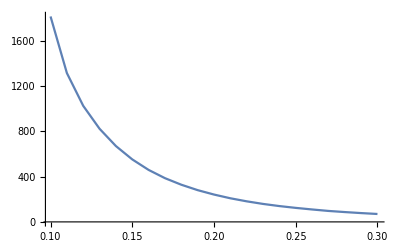

```mathematica
(*Построить график зависимости ϵ↦n^avg(ϵ)*)
(*След оператора Λ = Subscript[Λ, 1]*...*Subscript[Λ, d]*)
Λ=(∑_(k=1)^∞ λ[k])^d;
(*Начальное значение порога ошибки*)
start = 0.3;
(*Конечное значение порога ошибки*)
end = 0.1;
(*Шаг изменения порога ошибки*)
step=0.01;
(*Список для хранения сложности
аппроксимации в среднем от заданного порога ошибки*)
navgs=List[];
(*Список для хранения порогов ошибки*)
errors=List[];
(*Начальное значение количества элементов в частичной сумме*)
navg=1;
(*Начальное значение частичных сумм*)
PartAmount = RS[[navg, 1]];
(*Цикл по порогам ошибок*)
(*Первый порог ошибки равен start*)
(*Каждый последующий порог ошибки уменьшается на step*)
(*Пока порг ошибки не будет равен end*)
(*В данном случае частичная сумма не пересчитывается каждый раз, а учитывает прошлое значение*)
For[ϵ=start, ϵ ≥ end, ϵ = ϵ -step, 
(*Добавляем текущий порог ошибки в список порогов ошибок*)
AppendTo[errors,ϵ];
(*Пока частичная сумма по Subscript[λ, k] не станет больше либо равна (1-ϵ^2)*Λ*)
While[PartAmount < (1-ϵ^2)Λ  && navg < Length[RS],
navg= navg + 1;
PartAmount = PartAmount + RS[[navg, 1]];
]
(*Добавляем текущую сложности
аппроксимации в среднем в соответствующий список*)
AppendTo[navgs,navg];
];
For[i=1, i≤ Length[navgs],i++,
Print["n^avg(", errors[[i]], ") = ", R[[navgs[[i]],3]]]
]
Print[ListLinePlot[Table[{errors[[i]],navgs[[i]]},{i,1,Length[navgs]}]]];
```

```mathematica
ϵ=0.3;
maxt=500; (*Для разбиения (отрезка [0,1])^2 на равные интервалы*)
(*В качесте начального размера частичной суммы берем значение, найденое нами ранее*)
navg = navgs[[1]];
t[1]=t1;
t[2]=t2;
RV=Transpose[Table[RandomVariate[NormalDistribution[0,1],navg], {i,1,navg}]];
λk = List[];
ψk=List[];
kd=List[];
For[i=1,i≤ navg, i++,
AppendTo[λk, RS[[i,1]]];
AppendTo[ψk, RS[[i,2]]];
AppendTo[kd, RS[[i,3]]];
];
```

```mathematica
W[t1_,t2_]=∑_(k=1)^navg √λk[[k]]*ψk[[k]]*RV[[kd[[k,1]], kd[[k,2]]]];
```

```mathematica
maxt=100;
T=Table[{t1/maxt,t2/maxt,W[t1/maxt,t2/maxt]},{t1,0,maxt}, {t2,0,maxt}];
```

```mathematica
ListPlot3D[T,Mesh->All, InterpolationOrder->0]
```

-Graphics3D-